```mathematica
Name: Melissa Lee
Student ID: 105-128-234
Email: melissaloreleilee@gmail.com
Homework 2
```

x[t]=(a t^2)/2+t v0+x0

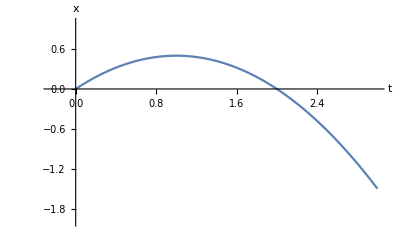

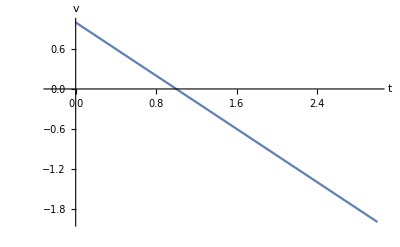

```mathematica
(*Problem 1*)
Remove["Global`*"] 
(*solve equation for x[t]*)
solution[t_] =DSolve[{x''[t]==a,x[0]==x0,x'[0]==v0},x[t],t][[1]]//FullSimplify;
Print["x[t]=",x[t]/.solution[t]];
(*set initial conditions*)
x0= 0;
v0=1;
a=-1;
(*parameters to get nice graph*)
thi =  3 ;
xmin=-2;
xmax=1;
tmin = -0.25;                   
tmax = thi;
range = { {tmin,tmax},{xmin,xmax}}; 
label1 = {"t","x"};
label2 = {"t","v"};
(*plot of x[t] vs t*)
Plot[Evaluate[x[t]/.solution[t]],{t,0,thi},PlotRange->range,AxesLabel->label1]
Plot[Evaluate[x'[t]/.solution'[t]],{t,0,thi},PlotRange->range,AxesLabel->label2]
```

```mathematica
(*Problem 2*)
Remove["Global`*"] 
(*eqations*)
diffEqn1[t_]=m x1''[t]+2 k x1[t]-k x2[t]==0;
diffEqn2[t_]=m x2''[t]+2 k x2[t]-k x1[t]==0;
(*initial conditions*)
init={x1'[0]==0,x2'[0]==0,x1[0]==0,x2[0]==L};
eqnList[t_]={diffEqn1[t],diffEqn2[t],init};
(*solve equations*)
solution[t_]=DSolve[eqnList[t],{x1,x2},t];
(*set variables*)
k=1;
m=1;
L=1;
(*parameters to get nice graph*)
thi = 5 2 π;
xmin=-1;
xmax=1;
tmin = -0.25;                   
tmax = thi;
range = { {tmin,tmax},{xmin,xmax}}; 
label = {"t","x"};
(*plot x1[t] and x2[t] vs t*)
 Plot[{Evaluate[x1[t]/.solution[t]],Evaluate[x2[t]/.solution[t]]},{t,0,thi},PlotRange->range,AxesLabel->label,PlotLabels->{x1,x2}]
```

-Graphics-

```mathematica
(*Problem 3*)
Remove["Global`*"] 
$Assumptions = {Element[{β, ω0, t},Reals] && β≥ 0 && ω0 > 0&& β< ω0};
(*equation*)
F[β_]=x''[t]+2 β x'[t]+ω0^2 x[t]==0;
(*initial conditions*)
init={x[0]==A0,x'[0]==0};
eqnList[β_]=Append[init,F[β]];
(*solve equations*)
solution[β_]:=DSolve[eqnList[β],x[t],t][[1]]//FullSimplify;
(*set variables*)
A0=5;
ω0=2 π;
(*parameters to get nice graph*)
thi = 2 π;
βlo=0;
βhi=4 π;
βstep=0.1; 
xmin=-5;
xmax=5;
tmin = -0.25;                   
tmax = thi;
range = { {tmin,tmax},{xmin,xmax}}; 
label = {"t","x"};
(*write x[t] so that it will return a value when β=ω0*)
x[β_,t_]:=
If[β==ω0,
x[t]/.solution[ω0],
x[t]/.solution[β],
x[t]/.solution[β]
]//Evaluate;
X[t]=x[t]/.solution[ω0];
Plot[{x[π/7,t],x[5 π/2,t],X[t]},{t,0,thi},PlotRange->range,AxesLabel->label,PlotLabels->{β=π/7,β=5 π/2,β=ω0}]
traj[β_]:= Plot[x[β,t],{t,0,thi},PlotRange->range,AxesLabel->label, PlotLabel->β]
Manipulate[traj[β],{β,βlo,βhi,βstep}]
```

-Graphics-

x[t]=-(a ⅇ^(-1/2 t (β+√(-4 k+β^2))) ((-1+ⅇ^(t √(-4 k+β^2))) β+(1+ⅇ^(t √(-4 k+β^2))-2 ⅇ^(1/2 t (β+√(-4 k+β^2)))) √(-4 k+β^2)))/(2 k √(-4 k+β^2))

x[t]=(ⅇ^(-1/2 β (t-f τ0)) (√(-4 k+β^2) Cosh[1/2 √(-4 k+β^2) (t-f τ0)] x[f τ0]+Sinh[1/2 √(-4 k+β^2) (t-f τ0)] (β x[f τ0]+2 x'[f τ0])))/(√(-4 k+β^2))

1

1

2

2/3

12

0.2

0.228166+1.00976×10^-16 ⅈ

2.21705+1.33227×10^-15 ⅈ

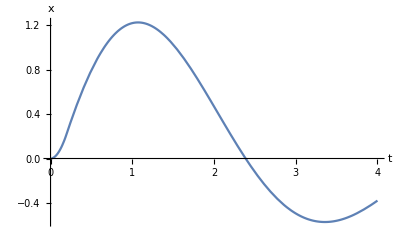

```mathematica
(*Problem 4*)
Remove["Global`*"] 
$Assumptions={Element[{b,k/m,t},Reals]&&β≥0&&(k/m)^0.5>0&&β<(k/m)^0.5};
(*solution of x[t] when 0<t<τ0*)
F[t_]=DSolve[{x''[t]+β x'[t]+k x[t]==a,x[0]==0,x'[0]==0},x[t],t][[1]]//FullSimplify;
Print["x[t]=",x[t]/.F[t]]
(*solution of x[t] when τ0<t*)
Func[t_]=DSolve[{X''[t]+k X[t]+β X'[t]==0,X[f τ0]==x[f τ0],X'[f τ0]==x'[f τ0]},X[t],t][[1]]//FullSimplify;
Print["x[t]=",X[t]/.Func[t]]
(*set variables*)
τ0=1
m=1
k=2
β=k/m/3
a=12
f=0.2
(*find where F and Func meet and plug values into Func*)
Evaluate[x[f τ0]/.F[f τ0]]
Evaluate[x'[f τ0]/.F'[f τ0]]
Func[t_]=DSolve[{X''[t]+β X'[t]+k X[t]==0,X[f τ0]==Evaluate[x[f τ0]/.F[f τ0]],X'[f τ0]==Evaluate[x'[f τ0]/.F'[f τ0]]},X[t],t][[1]]//FullSimplify;
(*parameters to get nice graph*)
label = {"t","x"};
(*plot x[t] from 0 to 4*)
Plot[Piecewise[{{x[t]/.F[t],0<t<f τ0},{X[t]/.Func[t],f τ0<t<4}}],{t,0,4},AxesLabel->label]
(*couldn't get the plot style thing to work maybe come back and try later*)
```